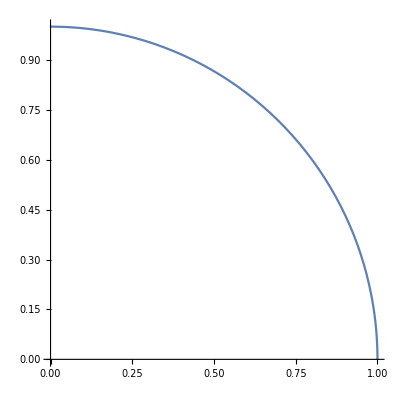

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,Pi/2}]
```

```mathematica
x[t_]:=Cos[t];
y[t_]:=Sin[t];

horiz=D[y[t],t];
crit1=Solve[horiz==0&&0≤t<2Pi]

vert=D[x[t],t];
crit2=Solve[vert==0&&0≤t<2Pi]

crit=Union[crit1,crit2][[All,1,2]]

dydx[t_]:=horiz/vert;
dydx[t]

between={Pi/4,3Pi/4,5Pi/4,7Pi/4};
dydx[t]/.t->between

pt[t_]:={{t->x[t]},{t->y[t]}}[[All,1,2]];
pt[#]&/@between
```

{{t→π/2},{t→(3 π)/2}}

{{t→0},{t→π}}

{0,π/2,π,(3 π)/2}

-Cot[t]

{-1,1,-1,1}

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
?:=
```

RowBox[{StyleBox["lhs", "TI"], ":=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"]. StyleBox["rhs", "TI"] is maintained in an unevaluated form. When StyleBox["lhs", "TI"] appears, it is replaced by StyleBox["rhs", "TI"], evaluated afresh each time.